# Les polynômes orthogonales

## Formule de Rodrigues - Les polynômes de Laguerre L_n^(α)(x)

```mathematica
Clear["Global`*"]
```

Les polynômes de Laguerre généralisés, notés L_n^(α)(x)sont, L_0^(α)(x),L_1^(α)(x),L_2^(α)(x),...,L_k^(α)(x). Dans cette notation  α>-1 est un nombre réel .Pour trouver les polynômes de Laguerre on doit choisir, α=0 :

```mathematica
α:=0
```

## Formule de Rodrigues

Les polynômes de Laguerre peut être définie par la formule de Rodrigues :

```mathematica
L[n_,α_,x_]:=1/(K[n] w[x])D[(w[x] g[x]^n), {x,n}]
```

### Initiation

```mathematica
table={{"Polynôme de degré 0, 1, ou 2", g[x_]=x}, {"Fonction poids", w[x_]=x^α ⅇ^-x}, {"Limite gauche d'intervalle d'orthogonalité", a=0}, {"Limite droite d'intervalle d'orthogonalité", b=+∞}, {"Multiplicateur de standardisation", K[n_]=n!}, {"Coefficient de x", κ[n_]=(-1)^n/(n!)}, {"Odre", k:=3}};
```

## Les polynômes

```mathematica
TableForm[Table[{n,L[n,α,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","L[n,α,x]"}}]
```

n | L[n,α,x]
0 | 1
1 | 1-x
2 | 1/2 (2-4 x+x^2)
3 | 1-3 x+(3 x^2)/2-x^3/6

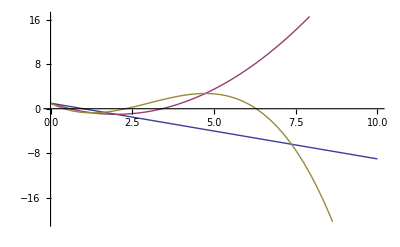

```mathematica
Plot[Evaluate[Table[L[n,α,x],{n,k}]],{x,0,10}]
```

## Orthogonalité

```mathematica
Table[∫_a^b w[x]L[n,α,x]L[n',α,x]ⅆx,{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

#### Carré de la norme

```mathematica
h[n_]=Simplify[((-1)^n κ[n]n!)/K[n]∫_a^b w[x] g[x]^n ⅆx,Assumptions->n∈Integers&&n≥0&&ν∈Reals&&ν>-1]
```

Gamma[1+n]/(n!)

```mathematica
Table[h[n]KroneckerDelta[n,n'],{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

## Normalization

```mathematica
L̃[n_,α_,x_]:=L[n,α,x]/(√h[n])
```

```mathematica
TableForm[Table[{n,L̃[n,α,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","L̃[n,α,x]"}}]
```

n | L̃[n,α,x]
0 | 1
1 | 1-x
2 | 1/2 (2-4 x+x^2)
3 | 1-3 x+(3 x^2)/2-x^3/6

## Orthonormalité

```mathematica
Table[∫_a^b w[x]L̃[n,α,x]L̃[n',α,x]ⅆx,{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

```mathematica
Table[KroneckerDelta[n,n'],{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

## Développement de la fonction f(x)

### La fonction à développer

```mathematica
f[x_] := Sin[x]
```

### Les coéfficients

```mathematica
Subscript[a, n_]:=∫_a^b w[x]L̃[n,α,x]f[x]ⅆx
```

```mathematica
Table[Subscript[a, n],{n,0,k}]
```

{1/2,0,-1/4,-1/4}

### Développement

```mathematica
fdev[x_]:=∑_(n=0)^5 Subscript[a, n] L̃[n,α,x]
```

## Représentation

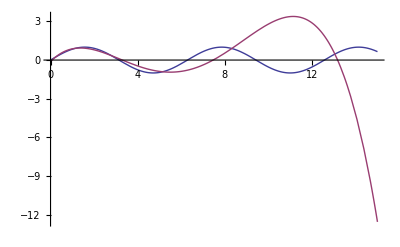

```mathematica
Plot[Evaluate[{f[x],fdev[x]}],{x,0,15},PlotRange->All]
```

```mathematica
Manipulate[Plot[Evaluate[{f[x],∑_(n=0)^k Subscript[a, n] L̃[n,α,x]}],{x,0,15},PlotRange->All],{k,1,10,1},ControlType->Setter]
```

## EDP

```mathematica
λ[n_]=n(K[1]D[L[1,α,x], {x,1}]+1/2(n-1)D[g[x], {x,2}])//FullSimplify
```

-n

Le n - ième polynôme de Laguerre satisfait l' équation différentielle suivante :

```mathematica
EDP=(D[(w[x] g[x]D[u[x], x]), x]-λ[n] w[x]u[x])/w[x]==0//FullSimplify
```

n u[x]+x u''[x]==(-1+x) u'[x]

```mathematica
DSolve[EDP,u[x],x]
```

{{u[x]→C[1] HypergeometricU[-n,1,x]+C[2] LaguerreL[n,x]}}

```mathematica
TableForm[Table[{n,L[n,α,x],LaguerreL[n,α,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","L[n,α,x]","LaguerreL[n,α,x]"}}]
```

n | L[n,α,x] | LaguerreL[n,α,x]
0 | 1 | 1
1 | 1-x | 1-x
2 | 1/2 (2-4 x+x^2) | 1/2 (2-4 x+x^2)
3 | 1-3 x+(3 x^2)/2-x^3/6 | 1-3 x+(3 x^2)/2-x^3/6